```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

### Sandbox




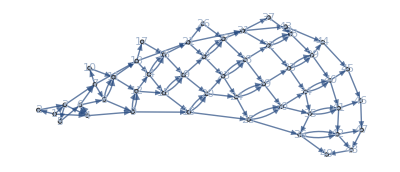
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp=SSS[{"AAB"->"AA","AA"->"ABA","B"->"A"},"AA",49];
```

```mathematica
sssTemp["Net"]
```

{1→2,1→3,2→3,3→4,1→4,3→5,5→6,4→6,4→6,3→7,6→7,7→8,6→8,8→9,4→9,7→10,10→11,8→11,8→11,11→12,9→12,9→12,7→13,11→13,13→14,12→14,14→15,12→15,15→16,9→16,13→17,17→18,14→18,14→18,18→19,15→19,15→19,19→20,16→20,16→20,13→21,18→21,21→22,19→22,22→23,20→23,23→24,20→24,24→25,16→25,21→26,26→27,22→27,22→27,27→28,23→28,23→28,28→29,24→29,24→29,29→30,25→30,25→30,21→31,27→31,31→32,28→32,32→33,29→33,33→34,30→34,34→35,30→35,35→36,25→36,31→37,37→38,32→38,32→38,38→39,33→39,33→39,39→40,34→40,34→40,40→41,35→41,35→41,41→42,36→42,36→42,31→43,38→43,43→44,39→44,44→45,40→45,45→46,41→46,46→47,42→47,47→48,42→48,48→49,36→49}

```mathematica
sssTemp["RulesUsed"]
```

{2,3,2,2,3,1,2,2,2,3,1,1,2,2,2,2,3,1,1,1,2,2,2,2,2,3,1,1,1,1,2,2,2,2,2,2,3,1,1,1,1,1,2,2,2,2,2,2,2}

```mathematica
StringLength/@sssTemp["Evolution"]
```

{2,3,3,4,5,5,4,5,6,7,7,6,5,6,7,8,9,9,8,7,6,7,8,9,10,11,11,10,9,8,7,8,9,10,11,12,13,13,12,11,10,9,8,9,10,11,12,13,14,15}